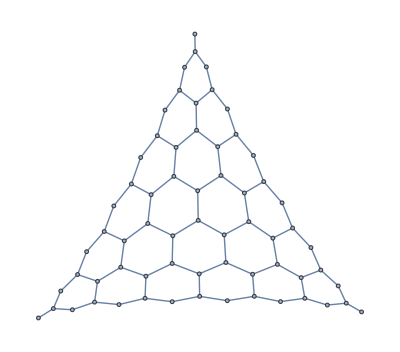

10834893628237824

```mathematica
makeGraphData[rows_]:=Join[
Flatten[Table[{y,x}<->{y,x-1},{y,0,rows-1},{x,1,2y}]],(*Horizontal edges*)
Flatten[Table[{y,2x+1}<->{y-1,2x},{y,0,rows-1},{x,0,y-1}]](*Vertical edges*)
]
makeGraph[rows_]:=Graph[makeGraphData[rows]]
g=makeGraph[8]
ChromaticPolynomial[g,3]
```